# 4.2 Stability exponents for a toy model

## We define a simple flow in polar coordinates on which to test that the Lyapunov exponent calculation works. Define the simple dynamics which has a stable fixed point and a limit cycle if .

## (a) Calculate the radius and the period of the limit cycle for . Give your result on the form .

To find the radius of a limit cycle one needs to know that its radius is constant, . So one can now solve 
		.
One receives  and , where off only  is a real solution.

To find the period  of the limit cycle one uses the angular velocity . Take the circumference of the limit cycle  and divide it by the angular velocity and then apply .

## Transform the dynamical system (1) into the Cartesian coordinates and , where and . Compare your result to the dynamical system with .

With  and  the system can be rewritten using Mathematica to the following equations:

```mathematica
ClearAll["Global`*"]

left1 = D[Sqrt[x1[t]^2 + x2[t]^2], t] // Simplify;
left2 = D[ArcTan[x1[t], x2[t]], t] // Simplify;

right1 = (Sqrt[x1[t]^2 + x2[t]^2]) * ( μ - (x1[t]^2 + x2[t]^2));
right2 = ω + ν*(x1[t]^2 + x2[t]^2);

eq1 = left1 == right1;
eq2 = left2 == right2;

sol1 = Solve[eq1,x1'[t]]//Simplify;
sol2 = Solve[eq2,x2'[t]]//Simplify;

(* Substitution of sol1 in sol2 *)
sol2WithSubstitution = sol2 /. sol1[[1]]//Simplify;
gleichung1 = x2'[t] == ν x1[t]^3+x1[t] (ω+2 ν x2[t]^2)+(x2[t] (-x1[t]^3+ω x2[t]+ν x2[t]^3+x1[t] (μ-2 x2[t]^2)-(x2[t] (-μ x2[t]+x2[t]^3+x2'[t]))/x1[t]))/x1[t];
solF1 = Solve[gleichung1,x2'[t]]//ExpandAll;

sol1WithSubstitution = sol1 /. solF1[[1]]//ExpandAll;
```

## b) Make a phase portrait of the dynamical system (2), showing a few representative trajectories. In the same figure, plot the limit cycle using a suitable representative trajectory. Upload your figure as .pdf or .png. Using StreamPlot[] is not acceptable. (0.5 points)

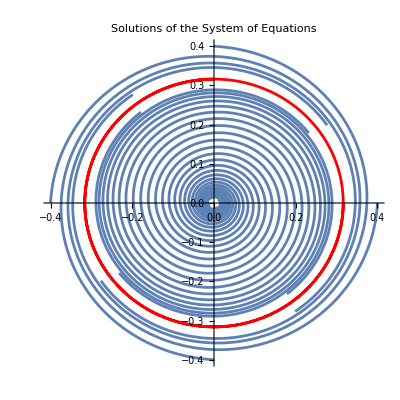

```mathematica
ClearAll["Global`*"]

(* Parameters for equations *)
mu = 1/10;
nu = 1;
omega = 1;

(* Define the system of equations *)
dotX1 = x1'[t] == mu*x1[t] + nu*x1[t]^2*x2[t] - x1[t]*x2[t]^2 - x1[t]^3 + nu*x2[t]^3 + omega*x2[t];
dotX2 = x2'[t] == -nu*x1[t]^3 - nu*x1[t]*x2[t]^2 - x1[t]^2*x2[t] - omega*x1[t] + mu*x2[t] - x2[t]^3;

system1 = {dotX1, dotX2};

FixedPoint1 = {0, 0};

t0 = 0;
tMax1 = 40;
tMax2 = 5;
tMax3 = 10;
eta1 = 0.01;
eta2 = 0.4;
eta3 = Sqrt[mu] - 0.0001;

(* Initial starting points with distance radius 0.2 from FixedPoint1 *)
initialConditions1 = {
   {x1[0] == FixedPoint1[[1]] + eta1, x2[0] == FixedPoint1[[2]] + eta1},
   {x1[0] == FixedPoint1[[1]] - eta1, x2[0] == FixedPoint1[[2]] + eta1},
   {x1[0] == FixedPoint1[[1]] + eta1, x2[0] == FixedPoint1[[2]] - eta1},
   {x1[0] == FixedPoint1[[1]] - eta1, x2[0] == FixedPoint1[[2]] - eta1}
};

(* Initial starting points with distance radius 1 from FixedPoint1 *)
initialConditions2 = {
   {x1[0] == FixedPoint1[[1]] + eta2, x2[0] == FixedPoint1[[2]]},
   {x1[0] == FixedPoint1[[1]] - eta2, x2[0] == FixedPoint1[[2]]},
   {x1[0] == FixedPoint1[[1]], x2[0] == FixedPoint1[[2]] + eta2},
   {x1[0] == FixedPoint1[[1]], x2[0] == FixedPoint1[[2]] - eta2}
};

ICLimitCycle = {x1[0] == FixedPoint1[[1]] + eta3, x2[0] == FixedPoint1[[2]]};

(* Use NDSolve for each set of initial conditions *)
sol1 = NDSolve[{system1, #}, {x1, x2}, {t, t0, tMax1}] & /@ initialConditions1;
sol2 = NDSolve[{system1, #}, {x1, x2}, {t, t0, tMax2}] & /@ initialConditions2;
sol3 = NDSolve[{system1, ICLimitCycle}, {x1, x2}, {t, t0, tMax3}];

(* Plot the solutions *)
TrajectoryPlot1 = ParametricPlot[Evaluate[{x1[t], x2[t]} /. #], {t, t0, tMax1}, 
     PlotStyle -> Automatic] & /@ sol1;
TrajectoryPlot2 = ParametricPlot[Evaluate[{x1[t], x2[t]} /. #], {t, t0, tMax2}, 
     PlotStyle -> Automatic] & /@ sol2;
TrajectoryPlot3 = ParametricPlot[Evaluate[{x1[t], x2[t]} /. sol3], {t, t0, tMax3}, 
     PlotStyle -> Red];  (* Fix: Set PlotStyle to Red *)

Show[TrajectoryPlot1, TrajectoryPlot2, TrajectoryPlot3,
 FrameLabel -> {"t", "Solution"}, 
 PlotLabel -> "Solutions of the System of Equations",
 PlotRange -> Full
 ]
```

## c) For which values of μ, ω and ν is the system (1) written in Cartesian coordinates identical to (2). Write your result as the vector .

This can be done using the calculation from right before b). The comparison of the coefficients yields:
	
	.

## From now on, we consider only the dynamical system (2). The deformation matrix M corresponding to (2) satisfies the differential equation with M(0)=I (the identity matrix) and . Set up a computer program to numerically solve the differential equation in the six variables and and .

## d) Starting on the limit cycle with and , plot all six quantities as functions of for one period of the limit cycle, . using a different colour for each quantity.

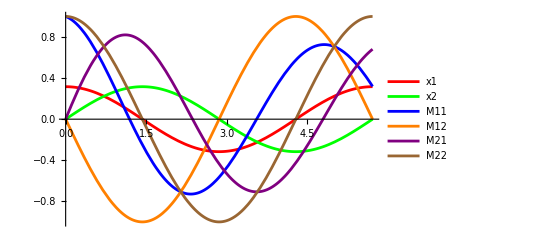

```mathematica
ClearAll["Global`*"]

μ = 1/10;
ω = 1;
ν = 1;

f1[x1_, x2_] := μ*x1[t] - ν*x1[t]^2*x2[t] - x1[t]*x2[t]^2 - x1[t]^3 - ν*x2[t]^3 - ω*x2[t];
f2[x1_, x2_] := ν*x1[t]^3 + ν*x1[t]*x2[t]^2 - x1[t]^2*x2[t] + ω*x1[t] + μ*x2[t] - x2[t]^3;

J11 = D[f1[x1, x2], x1[t]];
J12 = D[f1[x1, x2], x2[t]];
J21 = D[f2[x1, x2], x1[t]];
J22 = D[f2[x1, x2], x2[t]];

dotM11 = M11'[t] == J11*M11[t] + J12*M21[t];
dotM12 = M12'[t] == J11*M12[t] + J12*M22[t];
dotM21 = M21'[t] == J21*M11[t] + J22*M21[t];
dotM22 = M22'[t] == J21*M12[t] + J22*M22[t];

dotx1 = x1'[t] == μ*x1[t] - ν*x1[t]^2*x2[t] - x1[t]*x2[t]^2 - x1[t]^3 - ν*x2[t]^3 - ω*x2[t];
dotx2 = x2'[t] == ν*x1[t]^3 + ν*x1[t]*x2[t]^2 - x1[t]^2*x2[t] + ω*x1[t] + μ*x2[t] - x2[t]^3;

System = {dotM11, dotM12, dotM21, dotM22, dotx1, dotx2};
InitialConditions = {x1[0] == Sqrt[μ], x2[0] == 0, M11[0] == 1, M12[0] == 0, M21[0] == 0, M22[0] == 1};

t0 = 0;
tMax = 2*Pi/(ω+ν*μ);

sol = NDSolve[{System, InitialConditions}, {x1, x2, M11, M12, M21, M22}, {t, t0, tMax}];

x1Values = x1[t] /. sol[[1]];
x2Values = x2[t] /. sol[[1]];
M11Values = M11[t] /. sol[[1]];
M12Values = M12[t] /. sol[[1]];
M21Values = M21[t] /. sol[[1]];
M22Values = M22[t] /. sol[[1]];

PlotTrajectories = 
  Plot[Evaluate[{x1[t], x2[t], M11[t], M12[t], M21[t], M22[t]} /. sol[[1]]], {t, t0, tMax},
    PlotLegends -> {"x1", "x2", "M11", "M12", "M21", "M22"},
    PlotStyle -> {{Red, Thick}, {Green, Thick}, {Blue, Thick}, {Orange, Thick}, {Purple, Thick}, {Brown, Thick}},
    FrameLabel -> {{"Values", None}, {"Time", "Trajectories of x1, x2, M11, M12, M21, M22"}},
    PlotRange -> All
  ];
  
Show[PlotTrajectories]
```

## e) Give your numerical result for obtained in d) to 4 relevant digits accuracy. Write it as a matrix of the form .

```mathematica
(* Evaluate values at tMax *)
M11AtTMax = M11Values /. t -> tMax;
M12AtTMax = M12Values /. t -> tMax;
M21AtTMax = M21Values /. t -> tMax;
M22AtTMax = M22Values /. t -> tMax;

(* Display results with 4 relevant digits accuracy *)
sol = Round[{{M11AtTMax, M12AtTMax}, {M21AtTMax, M22AtTMax}}, 0.0001]//MatrixForm
```

(0.3191 | 0.
0.6809 | 1.)

## f) Calculate the stability exponents of separations and of the limit cycle from the eigenvalues of to 4 relevant digits accuracy. Write your results as the ordered vector with . (eigenvalue(M(T))

where

```mathematica
solMat = {{M11AtTMax, M12AtTMax}, {M21AtTMax, M22AtTMax}};

EV = Eigenvalues[solMat];

solTilde = Round[{1/tMax * Log[EV[[2]]],1/tMax * Log[EV[[1]]]},0.0001]
```

{-0.2,0.}

## g) Using what you know from all parts of this problem, calculate the deformation matrix M(T) analytically. Write your exact result (in Cartesian coordinates) in the form . Write exponentials as exp().

(matrix)


Now we want to transform them from polar to Cartesian. 
=  (matrix)
 here since M is expressed in polar,  is it as well. J^{-1}_G

```mathematica
ClearAll["Global`*"]

J11 = D[Sqrt[x1^2+x2^2],x1];
J12 = D[Sqrt[x1^2+x2^2],x2];
J21 = D[ArcTan[x1,x2],x1];
J22 = D[ArcTan[x1,x2],x2];

JG = {{J11,J12},{J21,J22}};
JGInv = Inverse[JG];

JakobiPol = {{μ-3r^2,0},{2*ν*r,0}};
JakExp = MatrixExp[JakobiPol*T];


T = 2*Pi/(ω+ν*μ);
x1 = Sqrt[μ];
x2 = 0;
ω = 1;
ν = 1;
μ = 1/10;
r = Sqrt[x1^2+x2^2];

solM = JGInv.JakExp.JG //Simplify
```

{{ⅇ^(-4 π/11),0},{1-ⅇ^(-4 π/11),1}}

## h) Compute the stability exponents of separations and of the limit cycle analytically. Write your result on the ordered form with .

Take the Eigenvalues of the  and do the analysis on the eigenvalues.

```mathematica
solm = Eigenvalues[solM];

Round[{1/T * Log[solm[[2]]],1/T * Log[solm[[1]]]},0.0001]
```

{-0.2,0.}